# Ion trap Simulation for ICL 2018 Ion trapping laboratory, QOLS group, ICL London, United Kingdom Jiyong Yu - Dept of Physics & Astronomy, Seoul National University, Republic of Korea Supervisor : Prof.Richard Thompson (02/07/2018 ~ 24/08/2018)

# Introduction 
In general, there are two types of ion traps : Penning traps and Paul traps
In this simulation, we calculate motion of ions in penning traps in various conditions.

# Simulators 
There are different modules for each number of ions.

SingleIon[B, offset, Vtrap, Vother, tEnd, timeStep, isLaseron]
DoubleIon[B, offset, Vtrap, Vother, tEnd, timeStep, isLaseron]
TripleIon[B, offset, Vtrap, Vother, tEnd, timeStep, isLaseron]

# Trapping method 
Trap potential 
- Between ring electrode and endcap : Vtrap[x_,y_,z_]:=V0/(2 d0^2)(2 z^2-x^2-y^2)
Because this is electric potential, by Earnshaw theorem there are no stable points  
But Penning trap uses DC magnetic field in z-direction, so there can be stable points in this condition.
In this condition, each ion has cyclotron & magnetron frequency and we can observe this motion.

                    -Graphics-              -Graphics-
           
Laser cooling 
- If Laser is slightly detuned below compared to the resonant frequency of ion’s transition frequency, we can cool down the ions.
This is called Doppler effect, and by appropriate parameters we get spiral motions for ion.
If laser is exactly pointed to center of trap, magnetron motion is not cooled because magnetron energy contributes negatively to total energy.
But if we give laser a slight offset from the center, magnetron motion is also cooled and we get cooled ion.

                     -Graphics-                 -Graphics-

Axialisation and Rotating wall technique
- By using axialisation or rotating wall technique, magnetron and cyclotron motions are coupled and exchange energy.
There are dipole & quadrupole rotating wall potential.
In the Prof.Richard Thompson’s lab, we use the quadrupole potential.
For multiple ions, we can get similar results.
                    -Graphics-                 -Graphics-
                    
 If there are axialisation or rotating wall potential, we can get laser cooling even if there are no offset!
             -Graphics-                -Graphics-
             
             
Multiple ions 
- For multiple ions, it is very similar to the single ion. (By considering coulomb force between ions)
In specific, for the axialisation or rotating wall technique,  each ion forms ion crystal and rotates resonantly to the potential! (half of cyclotron freq)
( In appropriate parameter )           

                   -Graphics-             -Graphics-

## Simulating modules

## - Common parameters of trap

### Basic parameters of Trap

```mathematica
ClearAll["Global`*"];
q = 1.6*10^-19;(* charge of electon *)
u = 1.66053904×10^-27;(* atomic mass *) 
m = 40.078*u;(*mass of calcium*)
ϵ = 8.854 * 10^-12(*permittivity of vaccum*);
r0 = 10*10^-3;(*ring electrode distance from origin*)
z0 = 10*10^-3;(*endcap electrode distance from origin*)
d0 =√((r0^2+2 z0^2)/2);(*characteristic distance from origin*)
h = 6.626*10^-34;(*Plank constant*)
S0 = 1;(*Saturation parameter of laser beam*)
w = 40 * 10^-6;(*width of gaussian*)
γ = 20*10^6;(*natural linewidth*);
c = 3 * 10^8;(*speed of light*)
λ = 400 * 10^-9;(*wavelength of laser beam*)
δ = -50 * 10^6;(*detuning of laser in lab frame*)
M = 1;(*Magnification factor*)
```

## - Single Ca+ Ion dynamics

### Trap PDE Solving by numerical method

```mathematica
SingleIon[B_,offset_,Vtrap_,Vother_,tEnd_,timeStep_,isLaseron_]:=Module[{ωc,FxTrap,FyTrap,Flaser,FxOther,FyOther,sol,trajectory,motion},
ωc=(q B)/m;(*cyclotron freuquency*)

FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)

FxOther[a_,b_,c_]:=-q*D[Vother[x,y,t],x]/.x->a/.y->b/.t->c;
FyOther[a_,b_,c_]:=-q*D[Vother[x,y,t],y]/.x->a/.y->b/.t->c;
(*Force by axialisation or rotating wall*)

sol = First[NDSolve[{x''[t]==ωc y'[t]+1/m(FxTrap[x[t],y[t]]+Flaser[x[t],y[t]*isLaseron]+FxOther[x[t],y[t],t]),y''[t]==-ωc x'[t]+ 1/m(FyTrap[x[t],y[t]]+FyOther[x[t],y[t],t]*isLaseron),x[0]==3.0*10^-5,y[0]==0.0*10^-5,x'[0]==0,y'[0]==10},{x[t],y[t]},{t,0,tEnd},StartingStepSize->timeStep,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*Solution of equations of motions*)

trajectory = Show[ParametricPlot[{x[t]/.sol,y[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for single ion",Bold,Italic,15],PlotPoints->2000],Graphics[Disk[{x[t]/.sol/.t->0,y[t]/.sol/.t->0},3.0*10^-6]]];

motion = Animate[Show[Graphics[{Black,Disk[{x[t]/.sol/.t->T,y[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for single ion",Bold,Italic,15]]],{T,0,tEnd},AnimationRate->(2.0*10^-6)/tEnd];

{sol,trajectory,motion}];
```

## - Two Ca+ Ions dynamics

### Trap PDE Solving by numerical method

```mathematica
DoubleIon[B_,offset_,Vtrap_,Vother_,tEnd_,timeStep_,isLaseron_]:=Module[
{ωc,FxTrap,FyTrap,Fcoulomb,F1x,F1y,F2x,F2y,Flaser,FxOther,FyOther,sol,trajectory,motion},
ωc=(q B)/m;(*cyclotron freuquency*)

FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Fcoulomb[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)); (*Coulomb force between two ions*)
F1x[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2));
F1y[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2));
F2x[x1_,y1_,x2_,y2_] = -F1x[x1,y1,x2,y2];
F2y[x1_,y1_,x2_,y2_] = -F1y[x1,y1,x2,y2];


Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)

FxOther[a_,b_,c_]:=-q*D[Vother[x,y,t],x]/.x->a/.y->b/.t->c;
FyOther[a_,b_,c_]:=-q*D[Vother[x,y,t],y]/.x->a/.y->b/.t->c;
(*Force by axialisation or rotating wall*)

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+1/m(FxTrap[x1[t],y1[t]] +F1x[x1[t],y1[t],x2[t],y2[t]]+Flaser[x1[t],y1[t]]*isLaseron+FxOther[x1[t],y1[t],t]),
y1''[t]==-ωc x1'[t]+ 1/m(FyTrap[x1[t],y1[t]] + F1y[x1[t],y1[t],x2[t],y2[t]]+FyOther[x1[t],y1[t],t]),
x2''[t]==ωc y2'[t]+1/m(FxTrap[x2[t],y2[t]]+F2x[x1[t],y1[t],x2[t],y2[t]]+Flaser[x2[t],y2[t]]*isLaseron+
FxOther[x2[t],y2[t],t]),
y2''[t]==-ωc x2'[t]+1/m(FyTrap[x2[t],y2[t]]+F2y[x1[t],y1[t],x2[t],y2[t]]+FyOther[x2[t],y2[t],t]),
x1[0]==-3.0*10^-5,y1[0]==-3.0*10^-5,x1'[0]==-30,y1'[0]==30,x2[0] == 3.0 * 10^-5,y2[0] == 3.0 * 10^-5,x2'[0]==30,y2'[0] == -30},{x1[t],y1[t],x2[t],y2[t]},{t,0,tEnd},StartingStepSize->timeStep,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*solution of the equations of motion*)

trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for two ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of two ions*)

motion=Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for two ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2.0*10^-6)/tEnd];(*motion of two ions*)

{sol,trajectory,motion}
];
```

## - Three Ca+ Ions dynamics

### Trap PDE Solving by numerical method

```mathematica
TripleIon[B_,offset_,Vtrap_,Vother_,tEnd_,timeStep_,isLaseron_]:=Module[
{ωc,FxTrap,FyTrap,F12,F13,F23,F1x,F1y,F2x,F2y,F3x,F3y,Flaser,FxOther,FyOther,sol,trajectory,motion},

ωc=(q B)/m;(*cyclotron freuquency*)

FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

F12[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)) (*Coulomb force between 1 & 2 ions*);
F13[x1_,y1_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x1)^2+(y3-y1)^2)) (*Coulomb force between 1 & 3 ions*);
F23[x2_,y2_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x2)^2+(y3-y2)^2)) (*Coulomb force between 1 & 3 ions*);
F1x[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2));
F1y[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2));
F2x[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F2y[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
F3x[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F3y[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)

FxOther[a_,b_,c_]:=-q*D[Vother[x,y,t],x]/.x->a/.y->b/.t->c;
FyOther[a_,b_,c_]:=-q*D[Vother[x,y,t],y]/.x->a/.y->b/.t->c;
(*Force by axialisation or rotating wall*)

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+1/m(FxTrap[x1[t],y1[t]]+F1x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]+Flaser[x1[t],y1[t]]*isLaseron+FxOther[x1[t],y1[t],t]),y1''[t]==-ωc x1'[t]+ 1/m(FyTrap[x1[t],y1[t]] + F1y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]+FyOther[x1[t],y1[t],t]),
x2''[t]==ωc y2'[t]+1/m(FxTrap[x2[t],y2[t]]+F2x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]+Flaser[x2[t],y2[t]]*isLaseron+FxOther[x2[t],y2[t],t]),
y2''[t]==-ωc x2'[t]+1/m(FyTrap[x2[t],y2[t]]+F2y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]+FyOther[x2[t],y2[t],t]),
x3''[t]==ωc y3'[t]+1/m(FxTrap[x3[t],y3[t]]+F3x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]+Flaser[x3[t],y3[t]]*isLaseron + FxOther[x3[t],y3[t],t]),
y3''[t]==-ωc x3'[t]+1/m(FyTrap[x3[t],y3[t]]+F3y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]] +  FyOther[x3[t],y3[t],t]),
x1[0]==-2.0*√3*10^-5,y1[0]==x1[0]/(√3),x1'[0]==-25.0,y1'[0]==-√3*x1'[0],x2[0] == 0.0 * 10^-5,y2[0] == -2*y1[0],x2'[0]==-2*x1'[0],y2'[0] == 0
,x3[0]==-x1[0],y3[0]==y1[0],x3'[0]==x1'[0],y3'[0]==√3*x3'[0]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,tEnd},StartingStepSize->timeStep,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*solution of the equations of motion*)

trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for three ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

,ParametricPlot[{x3[t]/.sol,y3[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Green},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]
,Graphics[Disk[{x3[t]/.sol/.t->0,y3[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of three ions*)

motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for three ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Green,Disk[{x3[t]/.sol/.t->T,y3[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-6)/tEnd];(*motion of three ions*)

{sol,trajectory,motion}];
```

## Simulations

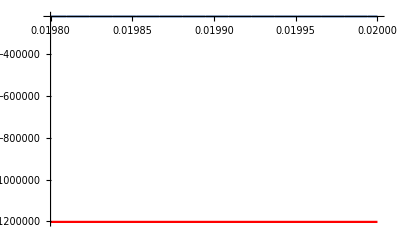

```mathematica
(* Simulation variables *)
B = 1.0;(* DC field in trap *)
offset = 0* 10^-6; (* Laser offset from the trap center *)
V0 = 30.0;(* Trap voltage *)
Va = 0.0;(* Axialisation voltage *)
Vr = 0.0; (* Rotating wall voltage *)
tEnd  = 20000*10^-6;
timeStep = 10*10^-9; (*TimeStep should be 1/100 of charcteristic time..like cyclotron period*)
isLaseron = 1;
ωc = (q B)/m;
Ω = -ωc/2;

(* Potentials in the trap *)
Vtrap[x_,y_,z_]:=V0/(2 d0^2)(2 z^2-x^2-y^2); (* Trap potential *)
Vnone[x_,y_,t_]:=0;
Vaxi[x_,y_,t_]:=Va/r0^2*(x^2-y^2)*Cos[2Ω t];(* Axialisation potential *)
VrotQuad[x_,y_,t_]:=Vr/r0^2*((x^2-y^2)*Cos[2Ω t] + 2x y Sin[2Ω t]);(* rotating wall Quadrupole potential *)
VrotDipo[x_,y_,t_]:=Vr/r0(x Cos[Ω t] + y Sin[Ω t]);(* rotating wall Dipole potential *)

(* Simulation result *)
result = DoubleIon[B,offset,Vtrap,Vnone,tEnd,timeStep,isLaseron];

sol = result[[1]];(* solution of ion trap system *)

θ[t1_]:=ArcTan[y1[t]/x1[t]]/.sol/.t->t1;
ω[t2_]:=D[θ[t1],t1]/.t1->t2;

p1 = Plot[ω[k],{k,0.99*tEnd,tEnd},PlotRange->All];
p2 = Plot[Ω,{k,0.99*tEnd,tEnd},PlotStyle->Red,PlotRange->All];
angularFreq = Show[p1,p2](* ploting equilibrium angular frequency vs ωc/2 *)
trajectory = result[[3]](* Animation of each ion in Trap *)
```